# Maximum Coherence Equality Violation - Upperbound

## Saved Computations

```mathematica
(*RegrasGroebner=<<savedRegrasGroebner`;
Ymatriz3=<<savedYmatrix3`;
(*Ymatriz4=<<savedYmatrix4`;*)
AllVariables3=<<savedAllVariables3`;
Ys=<<savedYs`;
onephoton=<<savedOnePhoton`;
{Y,X,S,flags}=<<savedOutputMaxBellViolation`;


ReplaceSolution=Thread[AllVariables3->Y[[1,1]]];
vars={x1,aj[x1],x2,aj[x2],x3,aj[x3],x4,aj[x4],x5,aj[x5],x6,aj[x6],x7,aj[x7],x8,aj[x8]};l
SetNonCommutative[{x1,x2,x3,x4,x5,x6,x7,x8}];*)
```

## Relevant Packages

```mathematica
vars={x1,aj[x1],x2,aj[x2],x3,aj[x3],x4,aj[x4],x5,aj[x5],x6,aj[x6],x7,aj[x7],x8,aj[x8]};
SetNonCommutative[{x1,x2,x3,x4,x5,x6,x7,x8}];
```

```mathematica
<<NC`;
<<NCAlgebra`;
<<NCGBX`;
<<SDP`;
```

You are using the version of NCAlgebra which is found in:

C:\Users\mario\NC\

You can now use "<< NCAlgebra`" to load NCAlgebra.

------------------------------------------------------------
NCAlgebra - Version 5.0.4
Compatible with Mathematica Version 10 and above

Authors:

  J. William Helton*
  Mauricio de Oliveira&

* Math, UCSD, La Jolla, CA
& MAE, UCSD, La Jolla, CA

with major earlier contributions by:

  Mark Stankus$ 
  Robert L. Miller#

$ Math, Cal Poly San Luis Obispo
# General Atomics Corp

Copyright: 
  Helton and de Oliveira 2017
  Helton 2002
  Helton and Miller June 1991
  All rights reserved.

The program was written by the authors and by:
  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,
  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,
  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 
  The beginnings of the program come from eran@slac.
  Considerable recent help came from Igor Klep.

Current primary support is from the 
  NSF Division of Mathematical Sciences.
  
This program was written with support from 
  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,
  UCSD Faculty Mentor Program,
  and US Department of Education.

For NCAlgebra updates see:

  www.github.com/NCAlgebra/NC
  www.math.ucsd.edu/~ncalg

------------------------------------------------------------

## Description of the Operators (skippable)

Variables:  (X_1,...,X_8)=(D_A^+,D_A^-,M_A^0,M_A^1,D_B^+,D_B^-,M_B^0,M_B^1)

```mathematica
vars={x1,aj[x1],x2,aj[x2],x3,aj[x3],x4,aj[x4],x5,aj[x5],x6,aj[x6],x7,aj[x7],x8,aj[x8]};
SetNonCommutative[{x1,x2,x3,x4,x5,x6,x7,x8}];
(* A side *)
rulesDec={x1**x1,x2**x1-x1,x2**x2-x2,x1**x2,aj[x1]**x1+aj[x2]**x2-1};
rulesPOVM ={x3+x4-1,x3**x4,x4**x3,x3**x3-x3,x4**x4-x4,aj[x3]-x3,aj[x4]-x4};

RulesA=Join[rulesDec,rulesPOVM];
RulesB=RulesA/.{x1->x5,x2->x6,x3->x7,x4->x8,x5->x1,x6->x2,x7->x3,x8->x4};

rulesCommuteAB=Flatten[Table[i**j-j**i,{i,{x1,x2,x3,x4,aj[x1],aj[x2],aj[x3],aj[x4]}},{j,{x5,x6,x7,x8,aj[x5],aj[x6],aj[x7],aj[x8]}}]];

Rules=Join[RulesA,RulesB,rulesCommuteAB];

Rules=DeleteCases[DeleteDuplicates[Join[Rules,Map[aj,Rules]]],0];
vars={x1,aj[x1],x2,aj[x2],x3,aj[x3],x4,aj[x4],x5,aj[x5],x6,aj[x6],x7,aj[x7],x8,aj[x8]};
ClearMonomialOrder[]
SetMonomialOrder[vars];
RegrasGroebner=NCMakeGB[Rules,50,ReturnRules->True];
(*RegrasGroebner>>"savedRegrasGroebner.m"*)
```

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: x1<x1^*<x2<x2^*<x3<x3^*<x4<x4^*<x5<x5^*<x6<x6^*<x7<x7^*<x8<x8^*

* Reduce and normalize initial set

> Initial set reduced to '51' out of '174' polynomials

* Computing initial set of obstructions

> MAJOR Iteration 1, 42 polys in the basis, 53 obstructions

* Found Groebner basis with 42 polynomials

* * * * * * * * * * * * * * * *

## Auxiliary Functions (skippable)

Funções Auxiliares

```mathematica
(* Words of Size At Most F_ from variables {x1,x2,x3,x4,x5,x6,aj[x1],aj[x2],aj[x3],aj[x4],aj[x5],aj[x6]} *)

WSAMN[F_]:=
WSAMN[F]=
If[F==1,Join[{1},vars],DeleteDuplicates[Flatten[Table[NonCommutativeMultiply[x,y],{x,Join[{1},vars]},{y,WSAMN[F-1]}]]]];

RemoverConstanteX[A_]:=RemoverConstanteX[A]=
If[StringPosition[ToString[A],"x"]=={},A,
If[StringPosition[ToString[A],"a"]!={},
ToExpression[StringJoin @  StringPart[ToString[A],StringPosition[ToString[A],"a"][[1,1]];;StringLength[ToString[A]];;1]],
ToExpression[StringJoin  @ StringPart[ToString[A],StringPosition[ToString[A],"x"][[1,1]];;StringLength[ToString[A]];;1]]]];



CasosReduzidos[n_]:=CasosReduzidos[n]=Join[{1},
DeleteCases[DeleteDuplicates[Map[RemoverConstanteX,Flatten[Table[FullReplaceRepeated[i]/.Plus->List,{i,WSAMN[n]}]]]],_Integer]];



FullReplaceRepeated[x_]:=NestWhile[
NCReplaceRepeated[NCE[#],RegrasGroebner]&,x,AlphabeticOrder[ToString[#],ToString[NCReplaceRepeated[NCE[#],RegrasGroebner]]]!=0&];


Matriz[k_]:=Matriz[k]=Map[FullReplaceRepeated,Table[aj[v]**w,{v,CasosReduzidos[k]},{w,CasosReduzidos[k]}],{2}];

variables[exp_]:=StringReplace[StringSplit[ToString[exp],"**"]," "->""];
break[exp_]:=Flatten[List[FullReplaceRepeated[exp]/.Plus->List]];

(* Turns -3aj[x1]**x2 -> {-3,{aj[x1],x2}} *)
constantAndVariables [val_]:=If[variables[val]=={"0"},{1,{"0"}},
{NCCoefficientList[val,vars][[1]],variables[val/NCCoefficientList[val,vars][[1]]]}];

(* Turns "aj[x1]"-> "01", "x1" -> "1",  Not used for varx_= 1 or 0 *)

turntonumber[varx_]:=If[StringPart[varx,1]=="x",StringPart[varx,2],StringJoin["0",StringPart[varx,5]],varx];

ExpressionToVariable[exp1_]:=If[constantAndVariables[exp1][[2]]=={"1"},constantAndVariables[exp1][[1]],
If[constantAndVariables[exp1][[2]]=={"0"},0,
constantAndVariables[exp1][[1]]*ToExpression[StringJoin["y",Map[turntonumber,constantAndVariables[exp1][[2]]]]]]];

VarPoly[expr_]:=VarPoly[expr]=Total[Map[ExpressionToVariable,break[expr]]];

Ymatriz[n_]:=Ymatriz[n]=Table[VarPoly[Matriz[n][[i,j]]],{i,Length[CasosReduzidos[n]]},{j,Length[CasosReduzidos[n]]}];

RemoverConstanteY[A_]:=
If[StringPosition[ToString[A],"y"]=={},A,
If[StringPosition[ToString[A],"\n"]!={},
StringJoin @  StringPart[ToString[A],StringPosition[ToString[A],"y"][[1,1]];;StringPosition[ToString[A],"\n"][[1,1]]-1;;1],
StringJoin  @ StringPart[ToString[A],StringPosition[ToString[A],"y"][[1,1]];;StringLength[ToString[A]];;1]]];

AllVariables[n_]:=Map[ToExpression,DeleteCases[DeleteDuplicates[Join[
Map[RemoverConstanteY,Apply[List,Ys]],
Map[RemoverConstanteY,Flatten[Ymatriz[n]/.Plus->List]]
]],_Integer]];
AllVariables3
```

AllVariables3

## SDP Problem (skippable) - generates new files

```mathematica
(* AllVariables[3]>>"savedAllVariables3.m"
Ymatriz[3]>>"savedYmatrix3.m"*)

AllVariables3=AllVariables[3];
Ymatriz3=Ymatriz[3];

Ys=VarPoly[FullReplaceRepeated[x3**x7+x4**x8+aj[x5]**(x3**x8+x4**x7)**x5+aj[x6]**(x3**x8+x4**x7)**x6+
aj[x1]**(x3**x8+x4**x7)**x1+aj[x2]**(x3**x8+x4**x7)**x2+aj[x1]**aj[x5]**(x3**x7+x4**x8)**x1**x5
+aj[x1]**aj[x6]**(x3**x7+x4**x8)**x1**x6+aj[x2]**aj[x5]**(x3**x7+x4**x8)**x2**x5+aj[x2]**aj[x6]**(x3**x7+x4**x8)**x2**x6]];

expected[epsilon_]:={VarPoly[FullReplaceRepeated[-aj[x1]**x1**aj[x5]**x5-aj[x2]**x2**aj[x6]**x6]]+epsilon};
(*
Ys>>"savedYs.m"

onephoton=Map[VarPoly, Table[FullReplaceRepeated[i],{i,
{aj[x1]**x1**aj[x5]**x5,aj[x2]**x2**aj[x6]**x6,-aj[x1]**x1**aj[x5]**x5,-aj[x2]**x2**aj[x6]**x6,aj[x2]**x2**aj[x5]**x5+aj[x1]**x1**aj[x6]**x6-1,-(aj[x2]**x2**aj[x5]**x5+aj[x1]**x1**aj[x6]**x6-1)}}]]

onephoton>>"savedOnePhoton.m"
*)
```

```mathematica
expected[0.01]
```

{-0.99+y2-2 y26+y6}

```mathematica
onephoton=Map[VarPoly, Table[FullReplaceRepeated[i],{i,
{aj[x1]**x1**aj[x5]**x5,aj[x2]**x2**aj[x6]**x6,-aj[x1]**x1**aj[x5]**x5,-aj[x2]**x2**aj[x6]**x6,aj[x2]**x2**aj[x5]**x5+aj[x1]**x1**aj[x6]**x6-1,-(aj[x2]**x2**aj[x5]**x5+aj[x1]**x1**aj[x6]**x6-1)}}]]
```

{1-y2+y26-y6,y26,-1+y2-y26+y6,-y26,-1+y2-2 y26+y6,1-y2+2 y26-y6}

```mathematica
expected2=Map[VarPoly, Table[FullReplaceRepeated[i],{i,
{aj[x1]**x1**aj[x5]**x5,aj[x2]**x2**aj[x6]**x6,-aj[x1]**x1**aj[x5]**x5,-aj[x2]**x2**aj[x6]**x6,aj[x2]**x2**aj[x5]**x5+aj[x1]**x1**aj[x6]**x6-1,-(aj[x2]**x2**aj[x5]**x5+aj[x1]**x1**aj[x6]**x6-1)}}]];
```

## Calculate the Bound

```mathematica
AllVariables3=AllVariables[3];
```

```mathematica
(*G={expected[1],Ymatriz3};*)
Ib=2.5;
G={Ys-Ib,Ymatriz3};
(*se demorar muito tempo considerar tirar -Ys *)
abc=SDPMatrices[-y2,G,AllVariables[3]];
```

```mathematica
{Y,X,S,flags}=SDPSolve[abc];
(*{Y,X,S,flags}>>"savedOutputMaxBellViolation.m"*)
```

Problem data:

* Dimensions (total):

- Variables             = 1418

- Inequalities          = 2

* Dimensions (detail):

- Variables             = {{1,1418}}

- Inequalities          = {1,85}

Method:

* Method                  = PredictorCorrector

* Search direction        = NT

Precision:

* Gap tolerance           = 1.×10^-9

* Feasibility tolerance   = 1.×10^-6

* Rationalize iterates    = False

Other options:

* Debug level             = 0

K     <B, Y>         mu  theta/tau      alpha     |X S|2    |X S|oo  |A* X-B|   |A Y+S-C|

-------------------------------------------------------------------------------------------

1 -3.900e-01  3.824e-01  2.531e-01  7.322e-01  3.618e+00  9.980e-01  3.528e-15  6.461e-16

2 -8.348e-01  1.408e-01  6.366e-02  6.561e-01  7.727e+00  9.006e-01  5.944e-15  1.171e-15

3 -9.176e-01  3.851e-02  1.545e-02  7.290e-01  9.750e+00  8.686e-01  1.881e-14  1.695e-15

4 -9.303e-01  1.335e-02  5.299e-03  6.534e-01  1.005e+01  9.001e-01  3.905e-14  8.047e-15

5 -9.378e-01  5.466e-03  2.165e-03  5.905e-01  1.023e+01  8.666e-01  1.059e-13  3.566e-14

6 -9.439e-01  1.850e-03  7.305e-04  6.615e-01  1.028e+01  8.662e-01  2.012e-13  1.735e-13

7 -9.466e-01  4.907e-04  1.931e-04  7.348e-01  1.037e+01  9.038e-01  5.379e-13  2.110e-12

8 -9.476e-01  9.323e-05  3.681e-05  8.100e-01  1.066e+01  8.641e-01  2.131e-12  2.743e-12

9 -9.478e-01  2.527e-05  1.002e-05  7.290e-01  1.074e+01  8.817e-01  1.047e-11  4.528e-12

10 -9.478e-01  8.689e-06  3.460e-06  6.561e-01  1.067e+01  9.404e-01  3.544e-11  4.173e-12

11 -9.478e-01  2.988e-06  1.195e-06  6.561e-01  1.060e+01  9.916e-01  5.032e-11  6.228e-12

12 -9.478e-01  2.052e-06  8.213e-07  3.133e-01  1.044e+01  9.921e-01  1.204e-10  7.491e-12

13 -9.478e-01  8.403e-07  3.374e-07  5.905e-01  1.028e+01  9.753e-01  1.668e-10  9.457e-12

14 -9.478e-01  4.786e-07  1.925e-07  4.305e-01  1.014e+01  9.928e-01  6.404e-10  1.327e-11

15 -9.478e-01  1.960e-07  7.912e-08  5.905e-01  1.001e+01  9.844e-01  1.149e-09  9.531e-12

16 -9.478e-01  1.116e-07  4.512e-08  4.305e-01  9.908e+00  9.695e-01  1.788e-09  9.468e-12

17 -9.478e-01  4.571e-08  1.854e-08  5.905e-01  9.795e+00  9.959e-01  3.777e-09  1.148e-11

18 -9.478e-01  3.525e-08  1.431e-08  2.288e-01  9.734e+00  9.957e-01  6.767e-09  1.152e-10

19 -9.478e-01  9.551e-09  3.880e-09  7.290e-01  9.638e+00  9.861e-01  2.055e-08  2.994e-10

20 -9.478e-01  9.473e-09  3.706e-09  2.762e-03  9.549e+00  9.730e-01  7.905e-08  4.614e-09

21 -9.478e-01  4.280e-09  1.673e-09  5.546e-01  9.646e+00  9.859e-01  9.514e-08  4.765e-09

LinearSolve::posdef: -- Message text not found -- ({«1»})

PrimalDual::HessianNotPositiveDefinite: Hessian is no longer positive definite

-------------------------------------------------------------------------------------------

* Algorithm interrupted before reaching requested precision

* Problem may be unfeasible

```mathematica
Y[[1,1]][[1]]
```

0.332712

```mathematica
Length[AllVariables3]
```

1418

```mathematica
Length[Y[[1,1]]]
```

1418

```mathematica
Ys
```

2+2 y01310575+2 y0131676-2 y01317+2 y2320575+2 y232676-2 y2327-2 y30575-2 y3676+2 y37

```mathematica
ReplaceSolution=Thread[AllVariables[3]->Y[[1,1]]];
```

```mathematica
Ys/4/.ReplaceSolution
```

1.

```mathematica
N[5/8]
```

0.625

```mathematica
MatrixRank[Ymatriz[3]/.ReplaceSolution]
```

85

```mathematica
MatrixRank[Ymatriz[2]/.ReplaceSolution]
```

32

```mathematica
Ymatriz3=<<savedYmatrix3`;
(*Ymatriz4=<<savedYmatrix4`;*)
AllVariables3=<<savedAllVariables3`;
Ys=<<savedYs`;
```

```mathematica
expected[epsilon_]:={VarPoly[FullReplaceRepeated[-aj[x1]**x1**aj[x5]**x5-aj[x2]**x2**aj[x6]**x6]]+epsilon};
```

```mathematica
f[varepsilon_]:=f[varepsilon]=Module[{},
G={expected[varepsilon],Ymatriz3};
abc=SDPMatrices[-Ys,G,AllVariables3];
{Y,X,S,flags}=SDPSolve[abc];
ReplaceSolution=Thread[AllVariables3->Y[[1,1]]];
{varepsilon,Ys/4/.ReplaceSolution}
];
```

```mathematica
Pontos={{0, 0.625121},
{0.01, 0.662739},
{0.02 ,0.679646},
{0.04 ,0.70462},
{0.05, 0.714988},
{0.1 ,0.756953},
{0.2, 0.818141},
{0.3, 0.864652},
{0.4, 0.902083},
{0.5, 0.932552},
{0.6,0.957026750},
{0.7,0.9759354568864623},
{0.8,0.9894005744172989} ,
{0.9,0.9974022187770072},
{1,1}
};
```

```mathematica
plot1=ListPlot[Pontos,PlotTheme-> "Scientific",Joined->True,PlotMarkers->Graphics@{Disk[{0,0},Scaled@0.010]}];
plot2 = Plot[x+(1-x)*0.5,{x,0,1}];
```

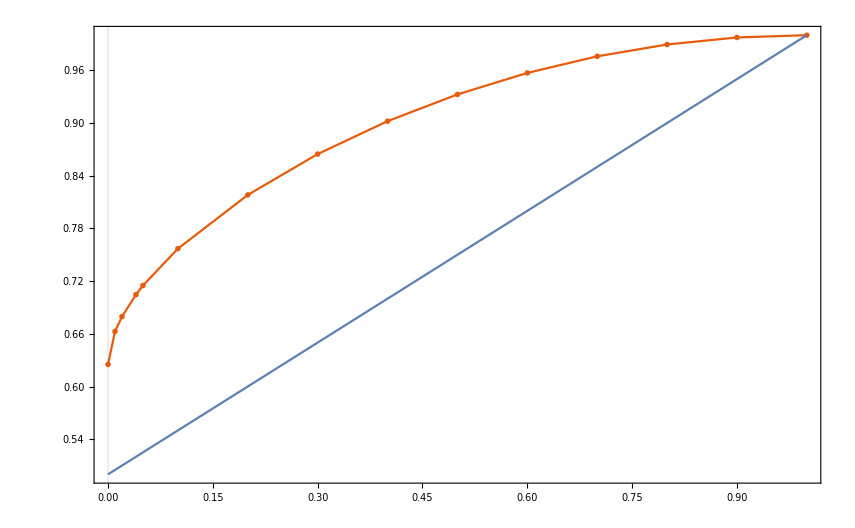

```mathematica
Show[plot1,plot2,PlotRange->{{0,1},{0.5,1}}]
```